```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 4/ohg6-hw4/";
(*~ Windows ~*)
(*main="/Users/Mikhail/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 4/ohg6-hw4/";*)

SetDirectory[main];
$Line=0;
```

# 1

## rk4

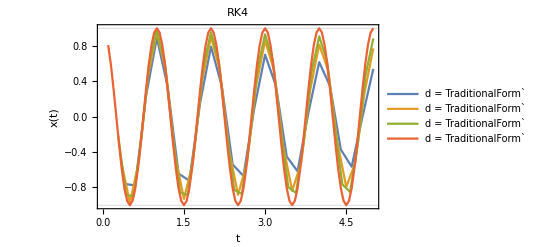

1/plots/rk4x.png

```mathematica
n=4;m={5,6,7,20};
datark4=Table[Import["1/data/data_rk4_"<>IntegerString[i,10,2]<>".txt","Data"],{i,1,n}];
ListLinePlot[datark4[[All,2;;,{1,2}]],GridLines->{None,{-1,1}},PlotRange->All,PlotLegends->Table["d = "<>ToString[Format["T"/i],TraditionalForm],{i,m}],PlotLabel->"RK4",Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","x(t)"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk4x.png",%]
```

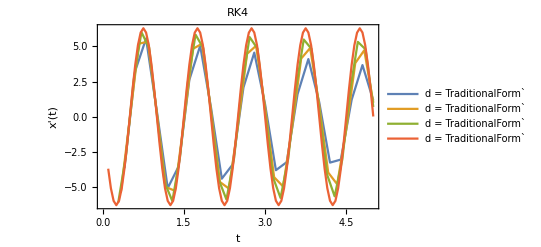

1/plots/rk4xp.png

```mathematica
ListLinePlot[datark4[[All,2;;,{1,3}]],GridLines->{None,{-2π,2π}},PlotRange->Automatic,PlotLegends->Table["d = "<>ToString[Format["T"/i],TraditionalForm],{i,m}],PlotLabel->"RK4",Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","x'(t)"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk4xp.png",%]
```

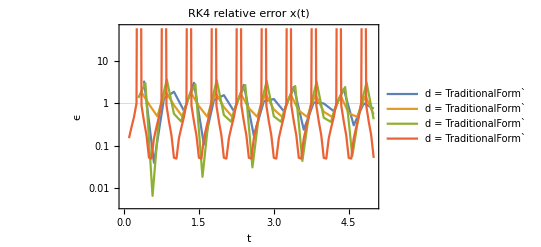

1/plots/rk4xerr.png

```mathematica
ListLogPlot[datark4[[All,2;;,{1,4}]],GridLines->{None,{1}},PlotRange->Automatic,PlotLegends->Table["d = "<>ToString[Format["T"/i],TraditionalForm],{i,m}],Joined->True,PlotLabel->"RK4 relative error x(t)",Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","ϵ"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk4xerr.png",%]
```

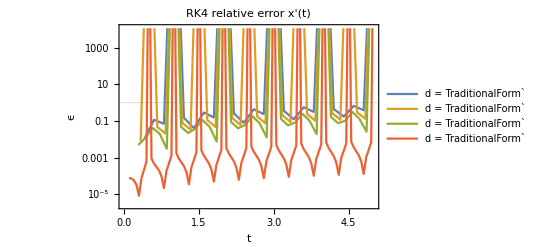

1/plots/rk4xperr.png

```mathematica
ListLogPlot[datark4[[All,2;;,{1,5}]],GridLines->{None,{1}},PlotRange->Automatic,PlotLegends->Table["d = "<>ToString[Format["T"/i],TraditionalForm],{i,m}],Joined->True,PlotLabel->"RK4 relative error x'(t)",Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","ϵ"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk4xperr.png",%]
```

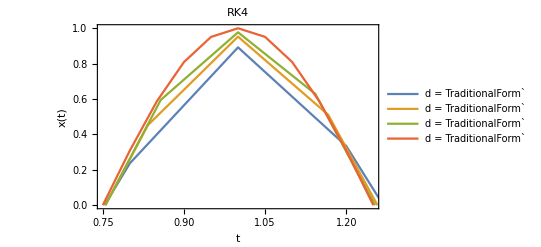

1/plots/rk4xzoom.png

```mathematica
ListLinePlot[datark4[[All,2;;,{1,2}]],PlotRange->{{3/4,5/4},{0,1}},PlotLegends->Table["d = "<>ToString[Format["T"/i],TraditionalForm],{i,m}],PlotLabel->"RK4",Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","x(t)"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk4xzoom.png",%]
```

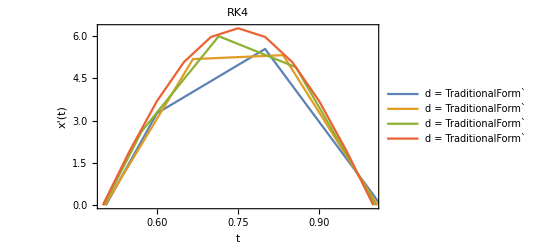

1/plots/rk4xpzoom.png

```mathematica
ListLinePlot[datark4[[All,2;;,{1,3}]],PlotRange->{{1/2,1},{0,2π}},PlotLegends->Table["d = "<>ToString[Format["T"/i],TraditionalForm],{i,m}],PlotLabel->"RK4",Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","x'(t)"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk4xpzoom.png",%]
```

## rk2

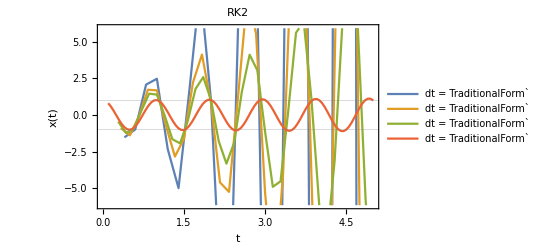

1/plots/rk2x.png

```mathematica
n=4;m={5,6,7,20};
datark2=Table[Import["1/data/data_rk2_"<>IntegerString[i,10,2]<>".txt","Data"],{i,1,n}];
ListLinePlot[datark2[[All,2;;,{1,2}]],GridLines->{None,{-1,1}},PlotRange->Automatic,PlotLegends->Table["dt = "<>ToString[Format["T"/i],TraditionalForm],{i,m}],PlotLabel->"RK2",Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","x(t)"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk2x.png",%]
```

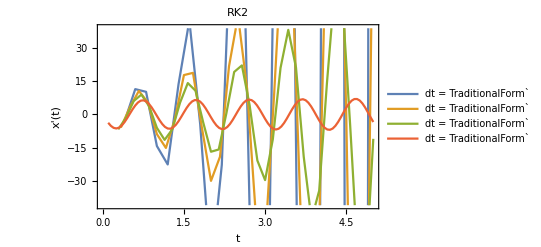

1/plots/rk2xp.png

```mathematica
ListLinePlot[datark2[[All,2;;,{1,3}]],GridLines->{None,{-2π,2π}},PlotRange->Automatic,PlotLegends->Table["dt = "<>ToString[Format["T"/i],TraditionalForm],{i,m}],PlotLabel->"RK2",Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","x'(t)"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk2xp.png",%]
```

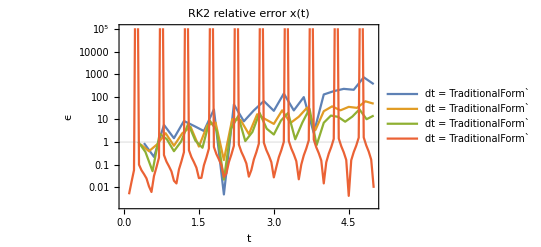

1/plots/rk2xerr.png

```mathematica
ListLogPlot[datark2[[All,2;;,{1,4}]],GridLines->{None,{1}},PlotRange->Automatic,PlotLegends->Table["dt = "<>ToString[Format["T"/i],TraditionalForm],{i,m}],Joined->True,PlotLabel->"RK2 relative error x(t)",Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","ϵ"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk2xerr.png",%]
```

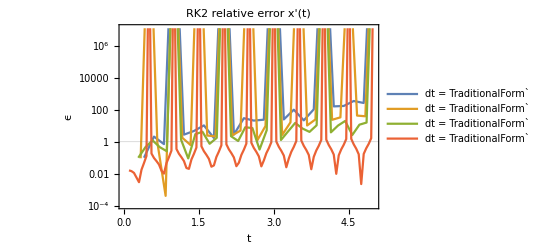

1/plots/rk2xperr.png

```mathematica
ListLogPlot[datark2[[All,2;;,{1,5}]],GridLines->{None,{1}},PlotRange->Automatic,PlotLegends->Table["dt = "<>ToString[Format["T"/i],TraditionalForm],{i,m}],Joined->True,PlotLabel->"RK2 relative error x'(t)",Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","ϵ"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk2xperr.png",%]
```

## rk45

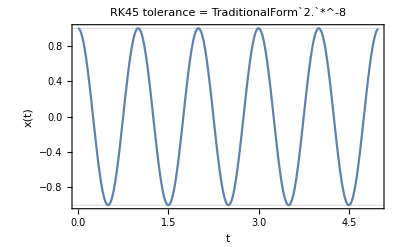

1/plots/rk45x.png

```mathematica
i=1;n=5;
For[i=1,i≤n,i++,
datark45[i]=Import["1/data/data_rk45_"<>ToString[i]<>".txt","Data"];
]
ListLinePlot[datark45[n][[2;;,{1,2}]],GridLines->{None,{-1,1}},PlotLabel->"RK45 tolerance = "<>ToString[datark45[5][[1,1]],TraditionalForm],Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","x(t)"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk45x.png",%]
```

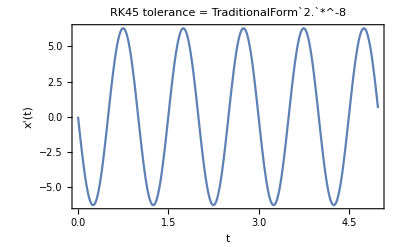

1/plots/rk45xp.png

```mathematica
ListLinePlot[datark45[n][[2;;,{1,3}]],GridLines->{None,{-2π,2π}},PlotLabel->"RK45 tolerance = "<>ToString[datark45[5][[1,1]],TraditionalForm],Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","x'(t)"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk45xp.png",%]
```

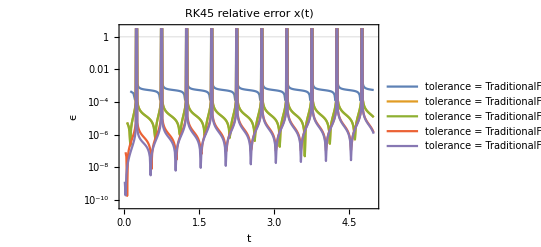

1/plots/rk45xerr.png

```mathematica
ListLogPlot[Table[datark45[i][[2;;,{1,4}]],{i,1,n}],GridLines->{None,{1}},PlotLabel->"RK45 relative error x(t)",PlotRange->Automatic,PlotLegends->Table["tolerance = "<>ToString[datark45[i][[1,1]],TraditionalForm],{i,1,n}],Joined->True,Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","ϵ"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk45xerr.png",%]
```

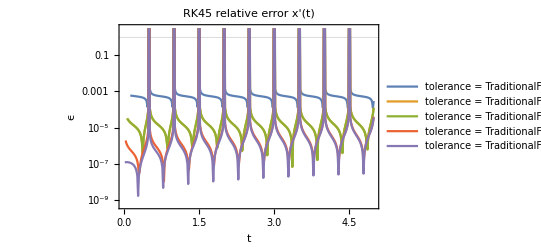

1/plots/rk45xperr.png

```mathematica
ListLogPlot[Table[datark45[i][[2;;,{1,5}]],{i,1,n}],GridLines->{None,{1}},PlotLabel->"RK45 relative error x'(t)",PlotRange->Automatic,PlotLegends->Table["tolerance = "<>ToString[datark45[i][[1,1]],TraditionalForm],{i,1,n}],Joined->True,Frame->True,Axes->False,FrameTicks->{{True,False},{True,False}},FrameLabel->{"t","ϵ"},LabelStyle->{FontFamily->Times,FontSize->12}]
Export["1/plots/rk45xperr.png",%]
```

# 2

```mathematica
Plot3D[x^2 y^2 Exp[-(x^2+y^2)],{x,-3,3},{y,-3,3},PlotRange->All,PlotStyle->Opacity[0.6],Mesh->None]
```

-Graphics3D-

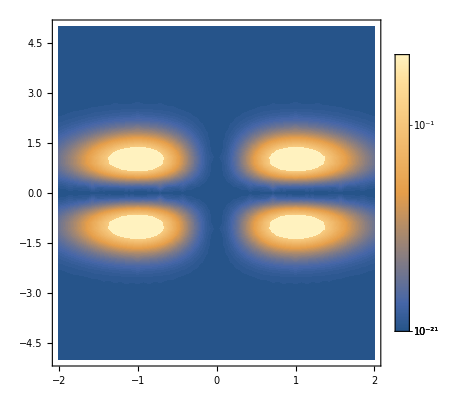

```mathematica
ContourPlot[x^2 y^2 Exp[-(x^2+y^2)],{x,-2,2},{y,-5,5},PlotLegends->Automatic,ContourStyle->None,Contours->50]
```

```mathematica
b=-0.2;Solve[10^-10==(b^2*y^2*Exp[-(b^2+y^2)])/(1/2*0.5*(0.5)^2),y,Reals]
```

{{y→-5.07834},{y→-0.0000127525},{y→0.0000127525},{y→5.07834}}

```mathematica
V[{x_,y_}]:=N[x^2 y^2 Exp[-(x^2+y^2)]]
```

```mathematica
Vt[x_]:=Table[N[(y[[1]])^2*(y[[2]])^2*Exp[-((y[[1]])^2+(y[[2]])^2)]],{y,x}]
```

```mathematica
vi={0.5,1.0,1.5};
```

## Repulsive

```mathematica
data=Table[Table[Import["2/repulsive/repulsive_data/data_"<>IntegerString[j,10,1]<>"_"<>IntegerString[i,10,3]<>".txt","Data"],{i,1,11}],{j,1,3}];
```

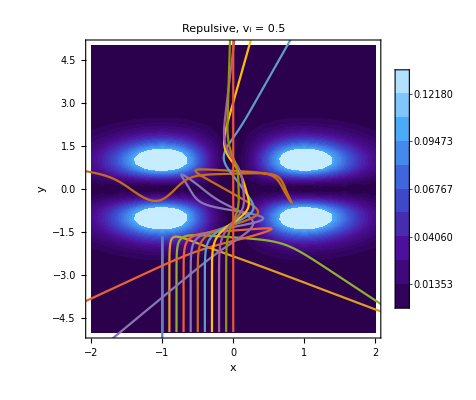

```mathematica
Table[Show[ContourPlot[x^2 y^2 Exp[-(x^2+y^2)],{x,-2,2},{y,-5,5},ColorFunction->(ColorData["DeepSeaColors"][#]&),Contours->20,ContourStyle->None,PlotLegends->Table[i,{i,0,Exp[-2],Exp[-2]/10}],FrameLabel->{"x","y"},PlotLabel->"Repulsive, v_i = "<>ToString[vi[[y]]]],ListLinePlot[data[[y,All,All,{2,3}]]],PlotRange->{{-2,2},{-5,5}},LabelStyle->{FontFamily->Times,FontSize->12}],{y,1,1,1}][[1]]
```

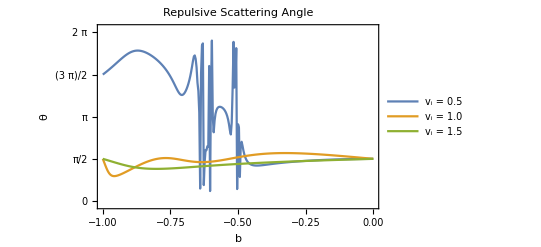

2/repulsive/scatt_repulsive.png

```mathematica
datascat=Table[Import["2/repulsive/repulsive_data/data_scatt_"<>IntegerString[j,10,1]<>".txt","Data"],{j,1,3}];
ListPlot[datascat[[All,All,{1,2}]],PlotRange->{-π/20,2π+π/20},FrameTicks->{{Table[i,{i,0,2π,π/2}],None},{Automatic,None}},FrameLabel->{{"θ",None},{"b",None}},Frame->True,FrameTicks->{{True,False},{True,False}},GridLines->{Table[i,{i,-1,0,0.1}],Table[i,{i,0,2π,π/2}]},LabelStyle->{FontFamily->Times,FontSize->12},PlotLabel->"Repulsive Scattering Angle",Joined->True,PlotLegends->{"v_i = 0.5","v_i = 1.0","v_i = 1.5"}]
Export["2/repulsive/scatt_repulsive.png",%]
```

## Attractive

```mathematica
data2=Table[Table[Import["2/attractive/data/data_"<>IntegerString[j,10,1]<>"_"<>IntegerString[i,10,3]<>".txt","Data"],{i,1,11}],{j,1,3}];
```

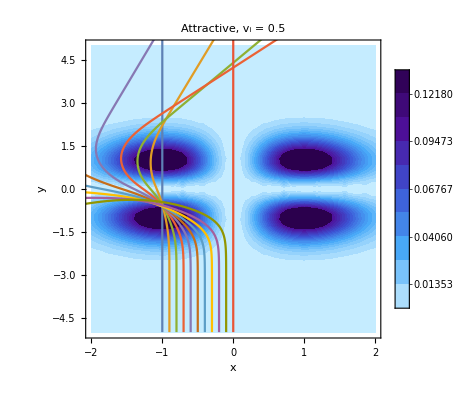

```mathematica
Table[Show[ContourPlot[x^2 y^2 Exp[-(x^2+y^2)],{x,-2,2},{y,-5,5},ColorFunction->(ColorData["DeepSeaColors"][1-#]&),Contours->20,ContourStyle->None,PlotLegends->Table[i,{i,0,Exp[-2],Exp[-2]/10}],FrameLabel->{"x","y"},PlotLabel->"Attractive, v_i = "<>ToString[vi[[y]]]],ListLinePlot[data2[[y,All,All,{2,3}]]],PlotRange->{{-2,2},{-5,5}},LabelStyle->{FontFamily->Times,FontSize->12}],{y,1,1,1}][[1]]
```

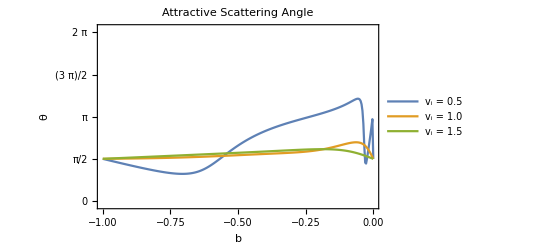

2/attractive/scatt_attractive.png

```mathematica
datascat2=Table[Import["2/attractive/attractive_data/data_scatt_"<>IntegerString[j,10,1]<>".txt","Data"],{j,1,3}];
ListPlot[datascat2[[All,All,{1,2}]],PlotRange->{-π/20,2π+π/20},FrameTicks->{{Table[i,{i,0,2π,π/2}],None},{Automatic,None}},FrameLabel->{{"θ",None},{"b",None}},Frame->True,FrameTicks->{{True,False},{True,False}},GridLines->{Table[i,{i,-1,0,0.1}],Table[i,{i,0,2π,π/2}]},LabelStyle->{FontFamily->Times,FontSize->12},PlotLabel->"Attractive Scattering Angle",Joined->True,PlotLegends->{"v_i = 0.5","v_i = 1.0","v_i = 1.5"}]
Export["2/attractive/scatt_attractive.png",%]
```

```mathematica
(*Manipulate[Show[Plot3D[x^2 y^2 Exp[-(x^2+y^2)],{x,-3,3},{y,-3,3},PlotRange->All,PlotStyle->Opacity[0.2],Mesh->None,ColorFunction->"Pastel"],ListPointPlot3D[data[[y,All,All,{2,3,7}]],PlotStyle->PointSize[0.001]],PlotRange->{{-3,3},{-3,3},{0,Exp[-2]}},ViewPoint->{-1,-2,1},Boxed->False],{y,1,3,1}]

Export["2/potential.gif",Table[Show[Plot3D[x^2 y^2 Exp[-(x^2+y^2)],{x,-3,3},{y,-3,3},PlotRange->All,PlotStyle->Opacity[0.2],Mesh->None,ColorFunction->"Pastel"],ListPointPlot3D[data[[1,All,All,{2,3,7}]],PlotStyle->PointSize[0.001]],ListPointPlot3D[data[[1,All,t,{2,3,7}]],PlotStyle->PointSize[0.02]],PlotRange->{{-3,3},{-3,3},{0,Exp[-2]}},ViewPoint->{-1,-2,1},Boxed->False],{t,1,Length[data[[1,1]]],60}],"DisplayDurations"->1/5]*)
```

## Export

```mathematica
For[j=1,j≤3,j++,
Export["2/repulsivemotion_rep_"<>IntegerString[j,10,1]<>".gif",Table[Show[ContourPlot[x^2 y^2 Exp[-(x^2+y^2)],{x,-2,2},{y,-5,5},ColorFunction->(ColorData["DeepSeaColors"][#]&),Contours->20,ContourStyle->None,PlotLegends->Table[i,{i,0,Exp[-2],Exp[-2]/10}],FrameLabel->{"x","y"},PlotLabel->"Repulsive, v_i = "<>ToString[vi[[j]]]],ListLinePlot[data[[j,All,All,{2,3}]]],ListPlot[Table[{data[[j,i,x,{2,3}]]},{i,1,11}],PlotStyle->PointSize[0.02]],PlotRange->{{-2,2},{-5,5}},LabelStyle->{FontFamily->Times,FontSize->12}],{x,1,Length[data[[1,1]]],60}],"DisplayDuration"->1/5,ImageSize->600]]
```

```mathematica
For[j=1,j≤3,j++,
Export["2/attractive/motion_att_"<>IntegerString[j,10,1]<>".gif",Table[Show[ContourPlot[x^2 y^2 Exp[-(x^2+y^2)],{x,-2,2},{y,-5,5},ColorFunction->(ColorData["DeepSeaColors"][1-#]&),Contours->20,ContourStyle->None,PlotLegends->Table[i,{i,0,Exp[-2],Exp[-2]/10}],FrameLabel->{"x","y"},PlotLabel->"Attractive, v_i = "<>ToString[vi[[j]]]],ListLinePlot[data2[[j,All,All,{2,3}]]],ListPlot[Table[{data2[[j,i,x,{2,3}]]},{i,1,11}],PlotStyle->PointSize[0.02]],PlotRange->{{-2,2},{-5,5}},LabelStyle->{FontFamily->Times,FontSize->12}],{x,1,Length[data2[[1,1]]],60}],"DisplayDuration"->1/5,ImageSize->600]]
```